## Draw the 1-stage Mark-3 robot cross section. This should be revolved about the z-axis

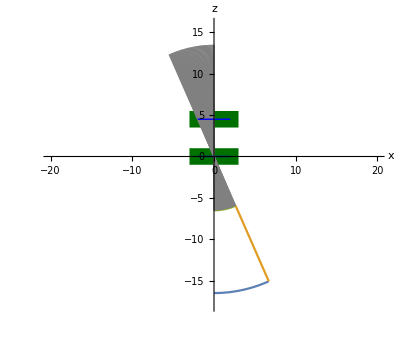

```mathematica
separation = 4.5;(*cm, distance between the two stage of MK3 *)
rad = 4(*cm, raduis of MK3 rotation*);
depthmin=6.5 (*cm, needle minimum insert length*);
depthmax = 10(*cm, needle maximum insert depth*);
range=2 (*cm, transition distance*);
halfStageDepth = 1;
needleTotalLen = 2 depthmax ;
ParametricPlot[{
(*arc at bottom*){(depthmin+depthmax)*Sin[t ArcTan[( range)/separation]],-(depthmin+depthmax)*Cos[t ArcTan[(range)/separation]]},
(*side slant*){(depthmin+t depthmax)*Sin[ArcTan[(range)/separation]],-depthmin*Cos[ ArcTan[(range)/separation]]-t depthmax*Cos[ ArcTan[(range)/separation]]},
(*true top*){depthmin Sin[ArcTan[ (range t)/separation]],-depthmin Cos[ArcTan[ (range t)/separation]]}
},{t,0,1},AxesLabel->{"x","z"},PlotRange-> {{-20,20},{-18,16}},Epilog->{Darker[Darker[Green]],Rectangle[{-range-halfStageDepth,-halfStageDepth},{range+halfStageDepth,+halfStageDepth}],Rectangle[{-range-halfStageDepth,separation-halfStageDepth},{range+halfStageDepth,separation+halfStageDepth}],
Gray,Table[p2={-range t,separation};(*p2 is the needle point on the top stage*)
p1 = {0,0};(*p1 is the needle point on the bottom stage*)
Line[{p1-(needleTotalLen-depthmin) Normalize[p1-p2],p1+depthmin Normalize[p1-p2]}],{t,0,1,.02}],
Blue, Line[{{-range,0},{range,0}}],Line[{{-range,separation},{range,separation}}]}]
```

## Draw the 2-stage Mark-3 robot cross section. This should be revolved about the z-axis

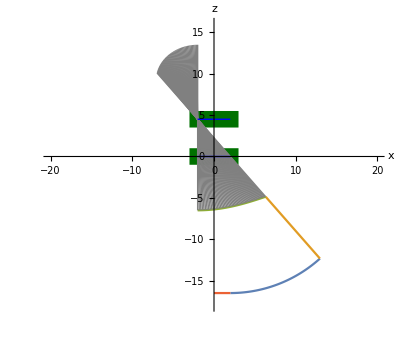

```mathematica
halfStageDepth = 1;
needleTotalLen = 2 depthmax ;
ParametricPlot[{
(*arc at bottom*){range +(depthmin+depthmax)*Sin[t ArcTan[(2 range)/separation]],-(depthmin+depthmax)*Cos[t ArcTan[(2range)/separation]]},
(*side slant*){range+(depthmin+t depthmax)*Sin[ArcTan[(2range)/separation]],-depthmin*Cos[ ArcTan[(2range)/separation]]-t depthmax*Cos[ ArcTan[(2range)/separation]]},
(*true top*){2range (t-0.5)+depthmin Sin[ArcTan[ (2 range t)/separation]],-depthmin Cos[ArcTan[ (2 range t)/separation]]},
{range t, -depthmin-depthmax}
},{t,0,1},AxesLabel->{"x","z"},PlotRange-> {{-20,20},{-18,16}},Epilog->{Darker[Darker[Green]],Rectangle[{-range-halfStageDepth,-halfStageDepth},{range+halfStageDepth,+halfStageDepth}],Rectangle[{-range-halfStageDepth,separation-halfStageDepth},{range+halfStageDepth,separation+halfStageDepth}],
Gray,Table[p2={-range,separation};(*p2 is the needle point on the top stage*)
p1 = {2range(t-0.5),0};(*p1 is the needle point on the bottom stage*)
Line[{p1-(needleTotalLen-depthmin) Normalize[p1-p2],p1+depthmin Normalize[p1-p2]}],{t,0,1,.02}],
Blue, Line[{{-range,0},{range,0}}],Line[{{-range,separation},{range,separation}}]}]
```

## Simulate the Mark3 robot, with 4 degrees of freedom in the control

```mathematica
separation = 4.5;(*cm, distance between the two stage of MK3 *)
rad = 4(*cm, raduis of MK3 rotation*);
depthmin=6.5 (*cm, needle minimum insert length*);
depthmax = 10(*cm, needle maximum insert depth*);
range=2 (*cm, transition distance*);
needlelen=2depthmax; (*cm, needle length*)
tr = 1/4; (*radius of torus, used because 3D art is easier to see than a line*)
toruses=ParametricPlot3D[ (*plot MK3 stage*)
{{0,0,0}+{(rad+tr Cos[v])Cos[t],(rad+tr Cos[v])Sin[t], +tr Sin[v]},
{0,0,separation}+{(rad+tr Cos[v])Cos[t],(rad+tr Cos[v])Sin[t], +tr Sin[v]}},
{t,0,2π},{v,0,2Pi},PlotStyle->Darker[Darker[Green]],
Mesh-> None,PlotRange-> {{-20,20},{-20,20},{-18,12}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
];

r4= RevolutionPlot3D[{ (*plot 4 DoF workspace*)
{2range (t-1/2)+depthmin*Sin[ ArcTan[(2 range t)/separation]],-depthmin*Cos[ ArcTan[(2 t range)/separation]]}(*top arc*),
{range +(depthmin+depthmax)*Sin[t ArcTan[(2 range)/separation]],-(depthmin+depthmax)*Cos[t ArcTan[(2range)/separation]]}(*bottom arc*),
{range+(depthmin+t depthmax)*Sin[ArcTan[(2range)/separation]],-depthmin*Cos[ ArcTan[(2range)/separation]]-t depthmax*Cos[ ArcTan[(2range)/separation]]}(*side slant*),
{range t, -depthmin-depthmax}
},{t,0,1},PlotRange->Automatic,PlotStyle->Directive[Blue,Opacity[0.5]]];

Manipulate[Module[{p1,p2,r1,r2,r3,empt
},
p1={d1 Cos[a1],d1 Sin[a1],0}; (*first layer MK3 stage*)
p2={d2 Cos[a2],d2 Sin[a2],separation};(*second layer MK3 stage*)
empt = Graphics3D[];
If[Show2DOFworkspace,
r1= ParametricPlot3D[p1-(depthmin+depth) Normalize[{d2v Cos[a2v],d2v Sin[a2v],separation}-p1], (*bottom arch*)
{a2v,0,π},{d2v,-2.5,2.5},
Mesh-> None,PlotRange-> {{-10,10},{-10,10},{-20,20}},PlotStyle->Directive[Red,Opacity[0.5]],
PlotRange-> {{-20-tr,20+tr},{-20-tr,20+tr},{-20-tr,20+tr}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
];
r2= ParametricPlot3D[p1-depthmin* Normalize[{d2v Cos[a2v],d2v Sin[a2v],separation}-p1],(*top arch*)
{a2v,0,π},{d2v,-2.5,2.5},
Mesh-> None,PlotStyle->Directive[Red,Opacity[0.5]],
PlotRange-> {{-20-tr,20+tr},{-20-tr,20+tr},{-20-tr,20+tr}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
];
r3= ParametricPlot3D[p1-d Normalize[{2.5 Cos[a2v], 2.5Sin[a2v],separation}-p1],(*side slant*)
{a2v,0,2π},{d,depthmin,depthmin+depth},
Mesh-> None,PlotStyle->Directive[Blue,Opacity[0.5]],
PlotRange-> {{-20-tr,20+tr},{-20-tr,20+tr},{-20-tr,20+tr}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
]];
Show[{toruses,If[Show2DOFworkspace,{r1,r2,r3},empt],If[Show4DOFworkspace,{r4},empt],
Graphics3D[
{Tube[{{rad*Cos[a1],rad*Sin[a1],0},{rad*Cos[a1+π],rad*Sin[a1+π],0}}],
Sphere[p1,1/2],
Tube[{{rad*Cos[a2],rad*Sin[a2],separation},{rad*Cos[a2+π],rad*Sin[a2+π],separation}}],
Sphere[p2,1/2],
(*needle*)Black,Tube[{p1-(depthmin+depth-0.01)Normalize[(p2-p1)],p1+(needlelen+4.5-(depthmin+depth-0.01))Normalize[(p2-p1)]},1/10]
}
]}
]],
Style["First layer MK3",12,Bold],Row[{Control@{{a1,0,"Rotation"},-π/2,π/2},"  ",
Control@{{d1,0,"Transition"},-range,range(*cm*)}}],
Style["Second layer MK3",12,Bold],Row[{Control@{{a2,0,"Rotation"},-π/2,π/2},"  ",
Control@{{d2,0,"Transition"},-range,range(*cm*)}}],
{{depth,5,"Insert depth"},0.01,depthmax(*cm*)},
Row[{Control@{Show2DOFworkspace,{True,False}},"   ",
Control@{Show4DOFworkspace,{False,True}}}]
]
```

## Simulate the Mark3 robot, with 4 degrees of freedom in the control with error

```mathematica
separation = 4.5;(*cm, distance between the two stage of MK3 *)
rad = 4(*cm, raduis of MK3 rotation*);
depthmin=6.5 (*cm, needle minimum insert length*);
depthmax = 10(*cm, needle maximum insert depth*);
range=2 (*cm, transition distance*);
error = 0.5; (*cm input error*)
errorl = 3; (*cm input error*)
needlelen=2depthmax; (*cm, needle length*)
tr = 1/4; (*radius of torus, used because 3D art is easier to see than a line*)
toruses=ParametricPlot3D[ (*plot MK3 stage*)
{{0,0,0}+{(rad+tr Cos[v])Cos[t],(rad+tr Cos[v])Sin[t], +tr Sin[v]},
{0,0,separation}+{(rad+tr Cos[v])Cos[t],(rad+tr Cos[v])Sin[t], +tr Sin[v]}},
{t,0,2π},{v,0,2Pi},
Mesh-> None,PlotRange-> {{-20,20},{-20,20},{-18,12}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
];

r4= RevolutionPlot3D[{ (*plot 4 DoF workspace*)
{2range (t-1/2)+depthmin*Sin[ ArcTan[(2 range t)/separation]],-depthmin*Cos[ ArcTan[(2 t range)/separation]]}(*top arc*),
{range +(depthmin+depthmax)*Sin[t ArcTan[(2 range)/separation]],-(depthmin+depthmax)*Cos[t ArcTan[(2range)/separation]]}(*bottom arc*),
{range+(depthmin+t depthmax)*Sin[ArcTan[(2range)/separation]],-depthmin*Cos[ ArcTan[(2range)/separation]]-t depthmax*Cos[ ArcTan[(2range)/separation]]}(*side slant*),
{range t, -depthmin-depthmax}
},{t,0,1},PlotRange->Automatic,PlotStyle->Directive[Blue,Opacity[0.5]]];

Manipulate[Module[{p1,p2,r1,r2,r3,r5,r6,r7,r8,empt
},
p1={d1 Cos[a1],d1 Sin[a1],0}; (*first layer MK3 stage*)
p2={d2 Cos[a2],d2 Sin[a2],separation};(*second layer MK3 stage*)
empt = Graphics3D[];
If[Show2DOFworkspace,
r1= ParametricPlot3D[p1-(depthmin+depth) Normalize[{d2v Cos[a2v],d2v Sin[a2v],separation}-p1], (*bottom arch*)
{a2v,0,π},{d2v,-2.5,2.5},
Mesh-> None,PlotRange-> {{-10,10},{-10,10},{-20,20}},PlotStyle->Directive[Red,Opacity[0.5]],
PlotRange-> {{-20-tr,20+tr},{-20-tr,20+tr},{-20-tr,20+tr}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
];
r2= ParametricPlot3D[p1-depthmin* Normalize[{d2v Cos[a2v],d2v Sin[a2v],separation}-p1],(*top arch*)
{a2v,0,π},{d2v,-2.5,2.5},
Mesh-> None,PlotStyle->Directive[Red,Opacity[0.5]],
PlotRange-> {{-20-tr,20+tr},{-20-tr,20+tr},{-20-tr,20+tr}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
];
r3= ParametricPlot3D[p1-d Normalize[{2.5 Cos[a2v], 2.5Sin[a2v],separation}-p1],(*side slant*)
{a2v,0,2π},{d,depthmin,depthmin+depth},
Mesh-> None,PlotStyle->Directive[Blue,Opacity[0.5]],
PlotRange-> {{-20-tr,20+tr},{-20-tr,20+tr},{-20-tr,20+tr}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
]];
If[Showerrorpropagation,
r5= ParametricPlot3D[p1-(depthmin+depth) Normalize[{d2v Cos[a2v],d2v Sin[a2v],separation}-p1], (*bottom arch*)
{a2v,0,π},{d2v,-error,error},
Mesh-> None,PlotRange-> {{-10,10},{-10,10},{-20,20}},PlotStyle->Directive[Red,Opacity[0.5]],
PlotRange-> {{-20-tr,20+tr},{-20-tr,20+tr},{-20-tr,20+tr}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
];
r6= ParametricPlot3D[p1-depthmin* Normalize[{d2v Cos[a2v],d2v Sin[a2v],separation}-p1],(*top arch*)
{a2v,0,π},{d2v,-error,error},
Mesh-> None,PlotStyle->Directive[Red,Opacity[0.5]],
PlotRange-> {{-20-tr,20+tr},{-20-tr,20+tr},{-20-tr,20+tr}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
];
r7= ParametricPlot3D[p1-d Normalize[{error Cos[a2v], error*Sin[a2v],separation}-p1],(*side slant*)
{a2v,0,2π},{d,depthmin,depthmin+depth},
Mesh-> None,PlotStyle->Directive[Blue,Opacity[0.5]],
PlotRange-> {{-20-tr,20+tr},{-20-tr,20+tr},{-20-tr,20+tr}},
AxesLabel->{"x","y","z"},LabelStyle->18,
ImageSize->500
];

];

Show[{toruses,If[Show2DOFworkspace,{r1,r2,r3},empt],If[Show4DOFworkspace,{r4},empt],If[Showerrorpropagation,{r5,r6,r7},empt],
Graphics3D[
{Tube[{{rad*Cos[a1],rad*Sin[a1],0},{rad*Cos[a1+π],rad*Sin[a1+π],0}}],
Sphere[p1,1/2],
Tube[{{rad*Cos[a2],rad*Sin[a2],separation},{rad*Cos[a2+π],rad*Sin[a2+π],separation}}],
Sphere[p2,1/2],
(*needle*)Black,Tube[{p1-(depthmin+depth-0.01)Normalize[(p2-p1)],p1+(needlelen+4.5-(depthmin+depth-0.01))Normalize[(p2-p1)]},1/10]
}
]}
]],
Style["First layer MK3",12,Bold],Row[{Control@{{a1,0,"Rotation"},-π/2,π/2},"  ",
Control@{{d1,0,"Transition"},-range,range(*cm*)}}],
Style["Second layer MK3",12,Bold],Row[{Control@{{a2,0,"Rotation"},-π/2,π/2},"  ",
Control@{{d2,0,"Transition"},-range,range(*cm*)}}],
{{depth,5,"Insert depth"},0.01,depthmax(*cm*)},
Row[{Control@{Show2DOFworkspace,{True,False}},"   ",
Control@{Show4DOFworkspace,{False,True}},"   ",
Control@{Showerrorpropagation,{False,True}}}]
]
```